```mathematica
SOI=Import["/users/pp/Desktop/soi.txt", "table"];
TSID=Import["/users/pp/Desktop/tsi.txt", "table"];
QBO=Import["/users/pp/Desktop/qbo20.txt", "table"];
QBO70=Import["/users/pp/Desktop/qbo.txt", "table"];
CW=Import["/users/pp/Desktop/cw.txt", "table"];
CW1=Import["/users/pp/Desktop/cw1_1930.txt", "table"];
CW0=Import["/users/pp/Desktop/cw1.txt", "table"];
NINO34=Import["/users/pp/Desktop/nino34ke.txt", "table"];
tahiti=Import["/users/pp/Desktop/tahiti.txt", "table"];
darwin=Import["/users/pp/Desktop/darwin0.txt", "table"];
```

80.1

2.33056

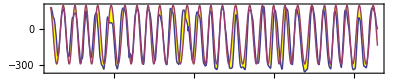

70.2574

6.47885

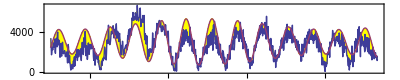

96.4942   0.

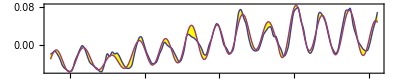

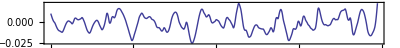

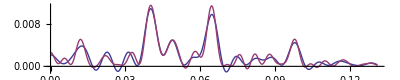

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 212;    WinHiFilter = 9;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=24; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)

QB=2.696; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.523*x+2.82]-0.07*Sin[0.12*x+0.2])+1.44] ; 
QBOM = Table[{1953.0+x, -240*qbo[73.0+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM];
2*Pi/QB
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]

CW =0.9698; cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
CWT = MeanFilter[CW1[[All,2]],3];
CWM = Table[{1880+i, 1770*cw[i-1.3]+3000},{i,50,133+2/12, 1/12}];
100*Correlation[CW1,CWM][[2,2]]
2*Pi/CW
ListLinePlot[{CW1,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]

(* Number 3 *)
sigmoid[x_] := 1/(1+Exp[6*(x-94.0)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.62*(2.7*Cos[HALE*(x-0.11)] + 0.7*Cos[HALE/2*(x-5.7)]+0.18*Cos[HALE/3*(x+3.8)]) +
                   (1-sigmoid[x])*0.99*(3.12*Cos[HALE2*(x-1.29)]+0.55*Cos[HALE/2*(x-7.0)])) +  
             2.42*Cos[2*Pi*x/153.1-1.0] +0.62*Cos[2*Pi*x/9.57+1.5] + 0.55*Cos[2*Pi*x/105.0+0.4] + 0*0.39*Cos[2*Pi*x/12.9+2.5]; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
OldCC = NewCC; NewCC = 100*Correlation[TSIT,TSIM][[2,2]]; Print[NewCC, "   ", NewCC-OldCC];
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}] 
SDIF = TSIT[[All,2]]-TSIM[[All,2]];  
ListLinePlot[SDIF, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/24},PlotRange->All,AspectRatio->0.2]
```

{char t,3.58018,-0.583746, Years from,1880.5,to,2013.33,CC,48.266,88.1783,39.9123}

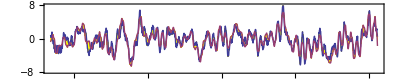

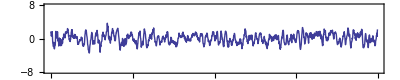

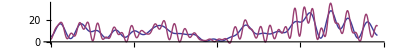

5.23599

-Graphics-

-Graphics-

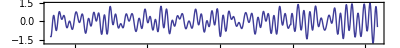

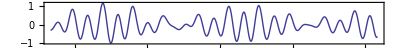

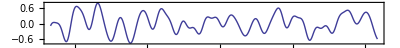

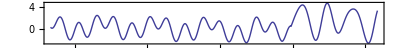

```mathematica
dilate[x_] := -0.15*Sin[0.076*x-0.45] - 0.13*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;   TSP = 21.91;  TR = 99.3;  CF = 3.08;  OSC := 9.091;  
TSI[x_] := 0.85*Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.8, 1.0] - 0.75*Cos[2*Pi/TSP*x+0.3] +
           If[x<TR, +0.18*tsi[x-1.8]-1.8*Cos[2*Pi/TSP*x+3.3],  -0.94*tsi[x-2.5]];
Hilla[x_] := CF + 0.23*tsi[x+0.5]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.6]-0.09*Cos[4*Pi/OSC*x+3]+0.18*Cos[Pi/(2*OSC)*x+3.7])-0.24*Cos[2*Pi*x/(3*OSC)-0.4];
Osc[x_] := 1.1*Tide9[x]-0.24*Cos[2*Pi/8.85*x+3] -0.1*Cos[2*Pi/8*x+5.5] +0.07*Cos[2*Pi/5*x+0.7] ;
qbw[x_] := +0.42*Cos[2*Pi/(QBW*3)*x+2.25]+0.45*Cos[2*Pi/QBW*x+2.6] -0.24*Cos[2*Pi/2.119*x-0.33]  +
                                     If[x<TR,-0.265*Cos[2*Pi/2.91*x-0.48],  -1*Cos[2*Pi/2.458*x-0.8]];
cwb[x_] := -0.48*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.28*Cos[2*Pi/5.79*x+1.4];  
RHS[x_] := 1*3.0*qbw[x]+1*3.2*cwb[x-0.23]-1*0.97*Cos[2*Pi/48*x+1]-1*5.4*Osc[x-1.2] + 1*1.11*TSI[x-0.02] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hilla[x]*R[[x*12]] - 0*0.11*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.72*RHS[x+dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.1/12
CWTT=ContinuousWaveletTransform[lhs[[All,2]]];  WaveletScalogram[CWTT]
CWTM=ContinuousWaveletTransform[rhs[[All,2]]];  WaveletScalogram[CWTM] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
ListLinePlot[{Table[{1880.0+x, cwb[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
ListLinePlot[{Table[{1880.0+x, Osc[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Tidal"}]
ListLinePlot[{Table[{1880.0+x, TSI[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"TSI"}]

(*qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.017*(TSI[i/12+3]))},{i,STRT,LNGTH,1}];
cwbb = Table[{1880+i/12, (0.0017*(1.5+cwb[i/12+1]))},{i,STRT,LNGTH,1}];
ListLinePlot[{CW,cwbb},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"cw","tsi"}]
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"tsi","model"}]
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposit
```

{3.58018 = char t,-0.212523 =err,1880.5  .. ,2013.33,CC,50.3801,50.4693,0.0891831}

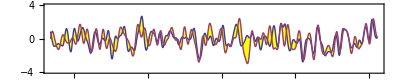

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 TR=52.0;  SHFT=-0;
SOLN=NDSolve[{y''[x]+Hilla[x]*y[x] == -11.4*RHS[x+0.5], 
                               y'[TR]==1.7, y[TR]==-1.3}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.05*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

{3.58018 = char t,-2.90528 =err,1880.5  .. ,2013.33,CC,58.1416,{188058.,156.905},{188000.,98.7632}}

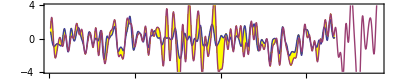

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 TR=52.0;  SHFT=-0;
SOLN=NDSolve[{y''[x]+Hilla[x]*y[x] == -1*RHS[x+0.5], 
                               y'[TR]==-2.5, y[TR]==0.1}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 1*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{3.58018 = char t,-2.63409 =err,1880.5  .. ,2013.33,CC,60.1923,60.2695,0.0771529}

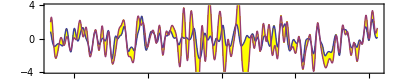

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 TR=51.9;  SHFT=0.1;
SOLN=NDSolve[{y''[x]+Hilla[x]*y[x] == -1.1*RHS[x+0.62], 
                               y'[TR]==-2.3, y[TR]==-0.0}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 1*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{3.58018 = char t,-1.00311 =err,1880.5  .. ,2013.33,CC,45.0011,47.6133,2.61226}

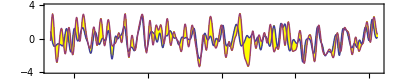

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 TR=9.9;  SHFT=0.0;
SOLN=NDSolve[{y''[x]+Hilla[x]*y[x] == -0.1*RHS[x+0.2], 
                               y'[TR]==+0.4, y[TR]==-0.2}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 7*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{3.58018 = char t,0.327878 =err,1880.5  .. ,2013.33,CC,26.6024,10.5464,-16.056}

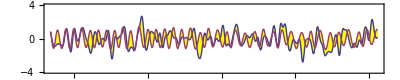

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
TR=60.0;  SHFT=0.1;
SOLN=NDSolve[{y''[x]+Hilla[x]*y[x] == -0.1*RHS[x+0.62], 
                               y'[TR]==1, y[TR]==-1.0}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 1*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{4.80487 = char t,0.0690674 =err,1880.5  .. ,2013.33,CC,50.356,50.356,1.42109×10^-14}

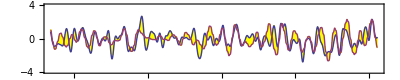

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 TR=52.5;  SHFT=0.55;
RHS[x_] := 1*3.0*qbw[x+0.11]+1*3.2*cwb[x-0.23]-1*0.97*Cos[2*Pi/48*x+1.3]-1*5.4*Osc[x-1.0] + 1.11*TSI[x-0.4] ;  
SOLN=NDSolve[{y''[x]+1.01*Hilla[x-0.3]*y[x]== -1*RHS[x+0.02], 
                               y'[TR]==-2.6, y[TR]==-0.3}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.2*(First[y[x-dilate[x]+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,4.68321,1.10481, Years from,1880.5,to,2013.33,CC,76.1537,76.6084,0.454798}

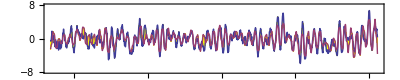

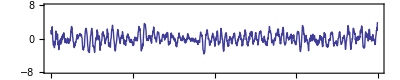

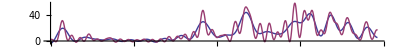

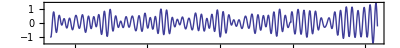

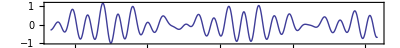

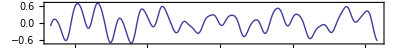

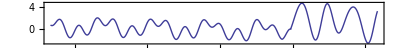

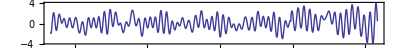

```mathematica
dilate[x_] := -0.15*Sin[0.076*x-0.45] - 0.13*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;   TSP = 21.91;  TR = 99.3;  CF = 1.8;  OSC := 9.091;  
TSI[x_] := 0.7*0.85*Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.7, 1.0] - 0.75*Cos[2*Pi/TSP*x+0.3] +
           If[x<TR, +0.18*tsi[x-1.8]-1.8*Cos[2*Pi/TSP*x+3.3],  -0.94*tsi[x-2.5]];
Hilla[x_] := CF + 0.11*tsi[x+0.5]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.6]-0.09*Cos[4*Pi/OSC*x+3]+0.18*Cos[Pi/(2*OSC)*x+3.7])-0.24*Cos[2*Pi*x/(3*OSC)-0.4];
Osc[x_] := 1.1*Tide9[x]-0.24*Cos[2*Pi/8.85*x+3] -0.08*Cos[2*Pi/8*x+5.5]  ;
qbw[x_] := +0.1*Cos[2*Pi/(QBW*3)*x+2.25]+0.45*Cos[2*Pi/QBW*x+2.6] -0.24*Cos[2*Pi/2.119*x-0.33]  +
                                     If[x<TR,-0.265*Cos[2*Pi/2.91*x-0.48],  -0.9*Cos[2*Pi/2.458*x-0.8]];
cwb[x_] := -0.48*cw[x+0.22]+0.22*cw[x/2+1.5] + 0.28*Cos[2*Pi/5.79*x+1.4];  
RHS[x_] := 1*2.5*qbw[x]+1*0.6*cwb[x-0.23]-1*1.1*Osc[x-1.2] + 1*0.34*TSI[x-0.02] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hilla[x]*R[[x*12]] - 0*0.11*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -1.2*RHS[x+dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
ListLinePlot[{Table[{1880.0+x, cwb[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
ListLinePlot[{Table[{1880.0+x, Osc[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Tidal"}]
ListLinePlot[{Table[{1880.0+x, TSI[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"TSI"}]
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
```

{4.68321 = char t,-0.0127159 =err,1880.5  .. ,2013.33,CC,{188058.,40.341},45.3819,{-188013.,5.04088}}

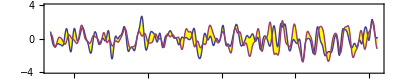

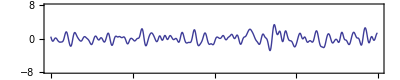

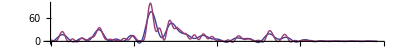

4.84814

```mathematica
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 TR=52.6;  SHFT=0.2;
SOLN=NDSolve[{y''[x]+0.93*Hilla[x-0.4]*y[x]== -6.6*RHS[x+0.0], 
                               y'[TR]==-0.2, y[TR]==1.3}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.13*(First[y[x-0*dilate[x]+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.108/12
```

{char t,3.56861,0.988305, Years from,1880.5,to,2013.33,CC,82.2201,67.2175,-15.0026}

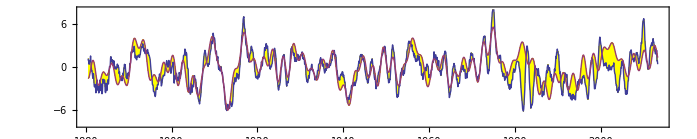

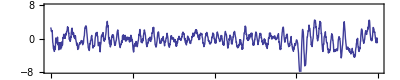

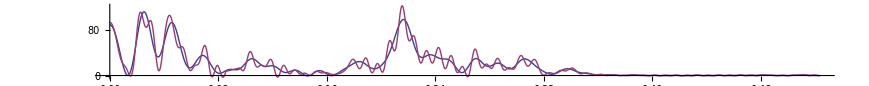

2.24721

```mathematica
dilate[x_] := -0.15*Sin[0.076*x-0.45] - 0.13*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;     TR = 200.3;  CF = 3.1;  OSC := 9.091;  
Hilla[x_] := CF + 0.3*tsi[x+0.0]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.6]-0.01*Cos[4*Pi/OSC*x+3]+0.18*Cos[Pi/(2*OSC)*x+3.7])-0.24*Cos[2*Pi*x/(3*OSC)-0.4];
Osc[x_] := 1.1*Tide9[x]-0.24*Cos[2*Pi/8.85*x+3] -0.1*Cos[2*Pi/8*x+5.5]  ;
qbw[x_] := +0.3*Cos[2*Pi/(QBW*3)*x+2.25]+0.5*Cos[2*Pi/QBW*x+2.7] -0.15*Cos[2*Pi/2.119*x-0.33]  +
                                     If[x<TR,-0.265*Cos[2*Pi/2.91*x-0.48],  -1*Cos[2*Pi/2.458*x-0.8]];
cwb[x_] := -0.48*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.28*Cos[2*Pi/5.79*x+1.4];  
RHS[x_] := 1*3.0*qbw[x]+1*3.2*cwb[x-0.23]-1*0.9*Cos[2*Pi/48*x+1]-1*5.1*Osc[x-1.2] + 0.1*tsi[x-0.3]-1.1*Cos[2*Pi/22*x+3.3] + 1.2*Cos[2*Pi/7.333*x+3.0] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hilla[x]*R[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.72*RHS[x+0*dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/6},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.233/12
```

{char t,4.81898,0.341171, Years from,1880.5,to,1980.,CC,72.608,72.8352,0.227189}

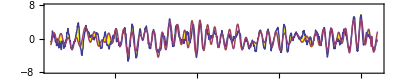

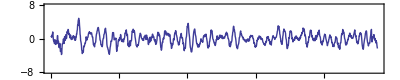

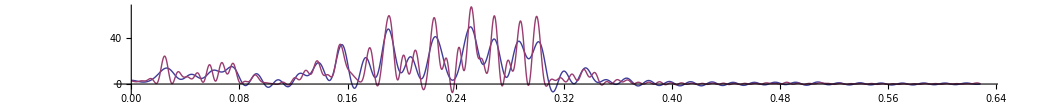

52.3599

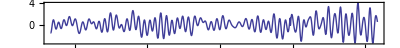

2.38039

```mathematica
dilate[x_] := -0.15*Sin[0.076*x-0.45] - 0.13*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 99.0;  CF = 1.7;  OSC := 9.09;  
Hilla[x_] := CF + 0.0*tsi[x+0.0]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.6]+0.14*Cos[Pi/(2*OSC)*x+3.7])-0.15*Cos[2*Pi*x/(3*OSC)-0.4];
Osc[x_] := 0.7*Tide9[x]-0.15*Cos[2*Pi/8.85*x+3]  ;
qbw[x_] := If[x<TR,1,0.56] *(+0.24*Cos[2*Pi/QBW*x+2.8] +0.13*Sin[2*Pi/2.246*x-0.0] -0.05*Cos[2*Pi/2.117*x-0.33] -0.06*Cos[2*Pi/3.58*x-1.5]-0.12*Cos[2*Pi/2.903*x-0.7]  +
                                     If[x<TR,0,  -0.9*Cos[2*Pi/2.458*x-0.88]*(1+0.5*Cos[2*Pi/5.78*x+0.9])]);
cwb[x_] := -0.48*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.0*Cos[2*Pi/5.79*x+1.4];  
RHS[x_] := 1*4.2*qbw[x-0.04]+1*0.4*cwb[x-0.23]-1*1.8*Osc[x-1.2] - 0.0*tsi[x-0.3]+0.2*Cos[2*Pi/52*x+4.3] + 0.2*Cos[2*Pi/7.333*x+3.0] ;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hilla[x]*R[[x*12]])},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -1.75*RHS[x+0*dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0.0,π/5},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.01/12
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
100.0/42.01
```

59.5508

2.33056

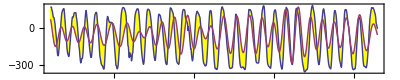

```mathematica
QBOM = Table[{1953.0+x, -400*(qbw[x+0.23])-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM];
2*Pi/QB
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

{4.81898 = char t,0.0751926 =err,1880.5  .. ,1980.,CC,53.8552,53.8552,0.}

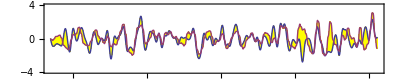

```mathematica
LNGTH=1600; STRT=12;
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=0.49;
(* RHS[x_] := 1*4.2*qbw[x+0.0]+1*0.55*cwb[x-0.23]-1*3.2*Osc[x-1.0] + 0.07*tsi[x-0.3]-0.2*Cos[2*Pi/22*x+3.3] + 0.3*Cos[2*Pi/7.333*x+3.0];  *)
SOLN=NDSolve[{y''[x]+1.29*y[x]== -90.3*RHS[x+0.05], 
                               y'[IC]==-35.0, y[IC]==+15.5}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.013*(First[y[x-dilate[x]+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{5.31026 = char t,0.573347 =err,1880.5  .. ,2013.33,CC,8.7645,-8.67044,-17.4349}

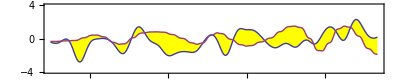

```mathematica
LNGTH=1600; STRT=1200;
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=0.45;
RHS[x_] := 1*4.2*qbw[x+0.0]+1*0.55*cwb[x-0.23]-1*3.2*Osc[x-1.0] + 0.07*tsi[x-0.3]-0.2*Cos[2*Pi/22*x+3.3] + 0.3*Cos[2*Pi/7.333*x+3.0];  
SOLN=NDSolve[{y''[x]+1.06*Hilla[x-0.0]*y[x]== -1.1*RHS[x+0.18], 
                               y'[IC]==0.0, y[IC]==+0.3}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.12*(First[y[x-dilate[x]+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```